# effect of variance “load” on hybrid fitness

distribution of hybrid traits assumed to be mutlivariate normal, centered at average between two parental optima with variance λ in each direction and no covariance

```mathematica
pxy=PDF[MultinormalDistribution[{(θx1+θx2)/2,(θy1+θy2)/2},{{λ,0},{0,λ}}],{x,y}]
```

ⅇ^(1/2 (-((x+1/2 (-θx1-θx2)) (2 x-θx1-θx2))/(2 λ)-((y+1/2 (-θy1-θy2)) (2 y-θy1-θy2))/(2 λ)))/(2 π √(λ^2))

the fitness functions of each parent environment

```mathematica
wxy1=2 π PDF[MultinormalDistribution[{θx1,θy1},{{1,0},{0,1}}],{x,y}]
wxy2=2 π PDF[MultinormalDistribution[{θx2,θy2},{{1,0},{0,1}}],{x,y}]
```

ⅇ^(1/2 (-(x-θx1)^2-(y-θy1)^2))

ⅇ^(1/2 (-(x-θx2)^2-(y-θy2)^2))

mean fitness of population on a peak with variance λ and its logarithm (chevin’s variance load)

```mathematica
Integrate[wxy1 PDF[MultinormalDistribution[{θx1,θy1},{{λ,0},{0,λ}}],{x,y}]/.θx1->0/.θy1->0,{x,-∞,∞},{y,-∞,∞},Assumptions->λ>0]
varload=-Log[%]
```

1/(1+λ)

-Log[1/(1+λ)]

we will use the above result to convert between variance λ and variance load.

plot mean hybrid fitness relative to mean hybrid fitness in absence of phenotypic variation across different amounts of variance for 3 amounts of divergent selection

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

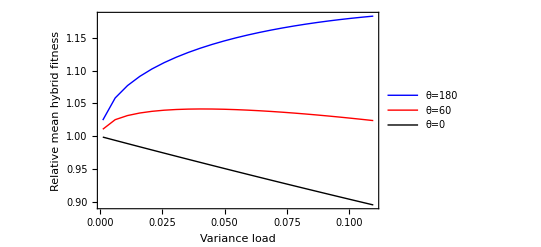

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.005}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Variance load",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend],Right],FrameStyle->Directive[FontSize->16]]
Export[NotebookDirectory[]<>"loadfit.pdf",%];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

save data for plotting in R

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{θs[[i]],varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.005}];
Flatten[%,1];
Export[NotebookDirectory[]<>"loadfit.csv",%,"CSV"];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

# higher dimension

distribution of hybrid traits assumed to be mutlivariate normal, centered at average between two parental optima with variance λ in each direction and no covariance

```mathematica
Clear[θ1,θ2]
n=10;
mean=Table[(θ1[i]+θ2[i])/2,{i,1,n}];
covarmat=λ IdentityMatrix[n];

vars=Table[z[i],{i,1,n}];

pxy=PDF[MultinormalDistribution[mean,covarmat],vars]
```

1/(32 π^5 √(λ^10))ⅇ^(1/2 (-((z[1]+1/2 (-θ1[1]-θ2[1])) (2 z[1]-θ1[1]-θ2[1]))/(2 λ)-((z[2]+1/2 (-θ1[2]-θ2[2])) (2 z[2]-θ1[2]-θ2[2]))/(2 λ)-((z[3]+1/2 (-θ1[3]-θ2[3])) (2 z[3]-θ1[3]-θ2[3]))/(2 λ)-((z[4]+1/2 (-θ1[4]-θ2[4])) (2 z[4]-θ1[4]-θ2[4]))/(2 λ)-((z[5]+1/2 (-θ1[5]-θ2[5])) (2 z[5]-θ1[5]-θ2[5]))/(2 λ)-((z[6]+1/2 (-θ1[6]-θ2[6])) (2 z[6]-θ1[6]-θ2[6]))/(2 λ)-((z[7]+1/2 (-θ1[7]-θ2[7])) (2 z[7]-θ1[7]-θ2[7]))/(2 λ)-((z[8]+1/2 (-θ1[8]-θ2[8])) (2 z[8]-θ1[8]-θ2[8]))/(2 λ)-((z[9]+1/2 (-θ1[9]-θ2[9])) (2 z[9]-θ1[9]-θ2[9]))/(2 λ)-((z[10]+1/2 (-θ1[10]-θ2[10])) (2 z[10]-θ1[10]-θ2[10]))/(2 λ)))

the fitness functions of each parent environment

```mathematica
opt1=Table[θ1[i],{i,1,n}];
opt2=Table[θ2[i],{i,1,n}];
wxy1=2 π PDF[MultinormalDistribution[opt1,IdentityMatrix[n]],vars]
wxy2=2 π PDF[MultinormalDistribution[opt2,IdentityMatrix[n]],vars]
```

(ⅇ^(1/2 (-(z[1]-θ1[1])^2-(z[2]-θ1[2])^2-(z[3]-θ1[3])^2-(z[4]-θ1[4])^2-(z[5]-θ1[5])^2-(z[6]-θ1[6])^2-(z[7]-θ1[7])^2-(z[8]-θ1[8])^2-(z[9]-θ1[9])^2-(z[10]-θ1[10])^2)))/(16 π^4)

(ⅇ^(1/2 (-(z[1]-θ2[1])^2-(z[2]-θ2[2])^2-(z[3]-θ2[3])^2-(z[4]-θ2[4])^2-(z[5]-θ2[5])^2-(z[6]-θ2[6])^2-(z[7]-θ2[7])^2-(z[8]-θ2[8])^2-(z[9]-θ2[9])^2-(z[10]-θ2[10])^2)))/(16 π^4)

plot mean hybrid fitness relative to mean hybrid fitness in absence of phenotypic variation across different amounts of variance for 3 amounts of divergent selection

```mathematica
Table[{z[i],-2,2},{i,1,n}]
```

{{z[1],-2,2},{z[2],-2,2},{z[3],-2,2},{z[4],-2,2},{z[5],-2,2},{z[6],-2,2},{z[7],-2,2},{z[8],-2,2},{z[9],-2,2},{z[10],-2,2}}

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θ1[1]=1;
Table[θ1[i]=0,{i,2,n}];
θ2[1]=Cos[θ*π/180];
θ2[2]=Sin[θ*π/180];
Table[θ2[i]=0,{i,3,n}];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.z[i_]->(θ1[i]+θ2[i])/2);

Table[{λ,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{z[1],-2,2},{z[2],-2,2},{z[3],-2,2},{z[4],-2,2},{z[5],-2,2},{z[6],-2,2},{z[7],-2,2},{z[8],-2,2},{z[9],-2,2},{z[10],-2,2},MinRecursion->50,MaxRecursion->100,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.11,0.025}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Segregation variance",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend],Right],FrameStyle->Directive[FontSize->16]]
Export[NotebookDirectory[]<>"loadfithigher.pdf",%];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65051×10^-42 and 1.65051×10^-42 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000390501 and 2.61439×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000365136 and 1.4485×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

$Aborted

$Aborted

ListPlot[$Aborted,Joined→True,PlotRange→All,Frame→{True,True,False,False},FrameLabel→{Segregation variance,Relative mean hybrid fitness},PlotStyle→{Directive[Thickness[Large],RGBColor[0,0,1]],Directive[Thickness[Large],RGBColor[1,0,0]],Directive[Thickness[Large],GrayLevel[0]]},PlotLegends→Placed[,Right],FrameStyle→Directive[FontSize→16]]

$Aborted

```mathematica
?WorkingPrecision
```

WorkingPrecision is an option for various numerical operations that specifies how many digits of precision should be maintained in internal computations.

```mathematica
flat[{x_}]:=x
```

```mathematica
Table[{z[i],-∞,∞},{i,1,n}]
flat[{%}]
```

{{z[1],-∞,∞},{z[2],-∞,∞},{z[3],-∞,∞}}

{{z[1],-∞,∞},{z[2],-∞,∞},{z[3],-∞,∞}}

```mathematica
Table[{z[i],-∞,∞},{i,1,n}]
ArrayReshape[%,{n,3}]
```

{{z[1],-∞,∞},{z[2],-∞,∞},{z[3],-∞,∞}}

{{z[1],-∞,∞},{z[2],-∞,∞},{z[3],-∞,∞}}

```mathematica
intvars
```

Sequence[{z[1],-∞,∞},{z[2],-∞,∞},{z[3],-∞,∞}]

```mathematica
?Sequence
```

Sequence[expr_1,expr_2,…] represents a sequence of arguments to be spliced automatically into any function.

save data for plotting in R

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={180,60,0};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{θs[[i]],varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.005}];
Flatten[%,1];
Export[NotebookDirectory[]<>"loadfithigher..csv",%,"CSV"];

Clear[θx1,θx2,θy1,θy2,θs,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

## higher dimension